# Wave equation in 1D Cartesian

## PHYS/MATH 4326 Prof. Katharine Long, TTU

Here we’ll solve u_tt=u_xx on x∈ [0,1] with boundary conditions u(0,t)=u(1,t)=0 and initial conditions u(x,0)=U_0(x), u_t(x,0)=V_0(x). We’ll take the initial displacement profile U_0(x) to be a triangle shape and the initial velocity V_0(x) to be zero.

Set the location of the plucking of the string

```mathematica
p = 1/5
```

1/5

```mathematica
Subscript[U, 0][x_]=Piecewise[{{x/p, 0<= x<= p},{(1-x)/(1-p),p<x<= 1}}]
```

Piecewise[{{5 x, 0≤x≤1/5}, {(5 (1-x))/4, 1/5<x≤1}}]

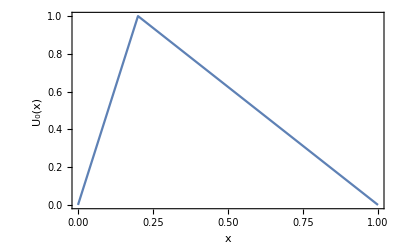

```mathematica
Plot[Subscript[U, 0][x],{x,0,1},Exclusions->None,FrameLabel->{x,"U_0(x)"}]
```

```mathematica
Subscript[V, 0][x_]=0
```

0

The solution is a sum of product solutions,

u(x,t)=Σ_(n=1)^∞v_n(x)(a_n cos(k_n t)+b_n sin(k_n t))

where k_n and  v_n(x) are eigenvalues and eigenvectors of a BVP arising from separation of variables, a_n is the n-th coefficient in the generalized Fourier expansion of the initial profile U_0(x), and k_n b_n is the n-the coefficient in the generalized Fourier expansion of V_0(x).

### Define a function to carry out the inner product

The IP is

⟨f,g⟩=∫_0^1 f(x)g(x) dx

```mathematica
IP[f_,g_]:=Integrate[f g,{x,0,1}]
```

Be sure to use deferred evaluation ( := ) when defining this, since the integration can’t be done until functions f(x) and g(x) are specified.

### Set the spatial eigenfunctions

We’re using BCs v(0)=v(1)=0. The eigenvalues and eigenfunctions are:

k_n=n π

v_n(x)=sin(k_n x)

```mathematica
Subscript[k, n_]=n Pi
```

π n

```mathematica
Subscript[v, n_][x_]=Sin[Subscript[k, n] x]
```

sin(π n x)

### Find the Fourier coefficients of the initial displacement and velocity profiles

The Fourier coefficients are

a_n=⟨v_n,U_0⟩/⟨v_n,.v_n⟩;      b_n=1/k_n⟨v_n,V_0⟩/⟨v_n,v_n⟩.

Here are functions to compute them,

```mathematica
Subscript[a, n_]=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

(5 (5 sin((π n)/5)-sin(π n)))/(4 π^2 n^2 (1/2-(sin(2 π n))/(4 π n)))

```mathematica
Subscript[b, n_]=1/Subscript[k, n]IP[Subscript[v, n][x],Subscript[V, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

0

### We have everything needed to form partial sums of the solution

The function uSum will form the partial sum through the M-th Fourier term.

```mathematica
uSum[M_,x_,t_]:=Sum[Subscript[v, n][x](Subscript[a, n] Cos[Subscript[k, n] t]+Subscript[b, n] Sin[Subscript[k, n] t]),{n,1,M}]
```

Form a few partial sums

```mathematica
u4[x_,t_]=uSum[4,x,t]
```

(25 √(5/8-(√5)/8) cos(π t) sin(π x))/(2 π^2)+(25 √(5/8+(√5)/8) cos(2 π t) sin(2 π x))/(8 π^2)+(25 √(5/8+(√5)/8) cos(3 π t) sin(3 π x))/(18 π^2)+(25 √(5/8-(√5)/8) cos(4 π t) sin(4 π x))/(32 π^2)

```mathematica
u16[x_,t_]=uSum[16,x,t];
```

```mathematica
v16[x_,t_]=D[u16[x,t],t];
```

```mathematica
u64[x_,t_]=uSum[64,x,t];
```

```mathematica
v64[x_,t_]=D[u64[x,t],t];
```

```mathematica
u128[x_,t_]=uSum[128,x,t];
```

```mathematica
v128[x_,t_]=D[u128[x,t],t];
```

```mathematica
u512[x_,t_]=uSum[512,x,t];
```

```mathematica
v512[x_,t_]=D[u512[x,t],t];
```

#### At t=0 we reproduce the initial profile

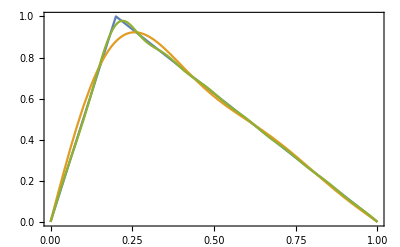

```mathematica
Plot[{Subscript[U, 0][x],u4[x,0],u16[x,0],u64[x,t]},{x,0,1},Exclusions->None]
```

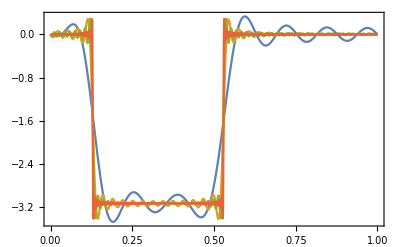

```mathematica
Plot[{v16[x,0.329],v64[x,0.329], v128[x,0.329],v512[x,0.329]},{x,0,1},Exclusions->None,PlotRange->All,PlotPoints->500]
```

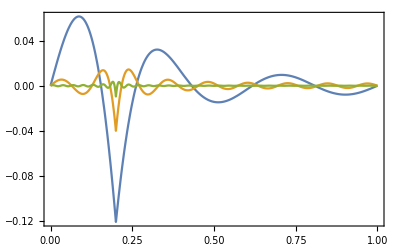

```mathematica
Plot[{u4[x,0]-Subscript[U, 0][x],u16[x,0]-Subscript[U, 0][x],u64[x,0]-Subscript[U, 0][x]},{x,0,1},Exclusions->None,PlotRange->All]
```

### Follow the evolution of the system

```mathematica
snapshot[t_]:=Plot[u128[x,t],{x,0,1},PlotRange->{-1,1},FrameLabel->{x,"Displacement",StringForm["t=``", t]}]
```

```mathematica
snapshotWithV[t_]:=Plot[{u128[x,t],v128[x,t]},{x,0,1},PlotRange->{-4,4},PlotStyle->{Black,Blue},PlotPoints->1000]
```

```mathematica
Animate[snapshot[t],{t,0,4},AnimationRate->.2,AnimationRunning->False,AnimationRepetitions->1]
```

```mathematica
Animate[snapshotWithV[t],{t,0,4},AnimationRate->.2,AnimationRunning->False,AnimationRepetitions->4]
```